# Monkeypox Parameter Optimization

## Initializing Data

```mathematica
Import["/Users/wagner.palacio/Documents/Projeto/Repos/SystemModeling/Projects/Monkeypox/SEIQREpidemiologyModel.m"];
Import["https://raw.githubusercontent.com/antononcube/SystemModeling/master/Projects/Coronavirus-propagation-dynamics/WL/EpidemiologyModelModifications.m"];
Import["https://raw.githubusercontent.com/antononcube/SystemModeling/master/Projects/Coronavirus-propagation-dynamics/WL/EpidemiologyModelingVisualizationFunctions.m"];
Import["https://raw.githubusercontent.com/antononcube/SystemModeling/master/WL/SystemDynamicsInteractiveInterfacesFunctions.m"];
$PlotTheme = "Scientific";
```

Importing from GitHub:  EpidemiologyModels.m

```mathematica
cievsPEData := Import["https://raw.githubusercontent.com/palaciowagner/SystemModeling/master/Projects/Monkeypox/data/Pernambuco/Monkeypox%20-%20Pernambuco.csv", 
   "Dataset", "HeaderLines" -> 1];
owdPEData := Import["https://raw.githubusercontent.com/palaciowagner/SystemModeling/master/Projects/Monkeypox/data/OWD/latest_deprecated.csv", "Dataset", "HeaderLines" -> 1];
```

```mathematica
dateFormat = {"Day", "/", "Month", "/", "Year"};
PEdataMap = cievsPEData // Normal;
owdPEDataMap = Query[Select[StringContainsQ[ #Country, "Brazil"] && StringContainsQ[#Location, "Pernambuco"] && StringContainsQ[#Status, "confirmed"]&]] @ owdPEData;
```

```mathematica
pernambucoPopulation = QuantityMagnitude[9674793]; 
recifePopulation =  QuantityMagnitude[1661017]; 
maleInfected = 82.6/100;(*Cievs/PE. Dados atualizados em 10.11.2022, 15h.*)
estimatedInitialSusceptiblePopulation = ((recifePopulation/pernambucoPopulation)*maleInfected)*recifePopulation
```

235552.

```mathematica
groupedByDateOWD = GroupBy[Normal[owdPEDataMap], FromDateString[#"Date_confirmation", {"Year", "-", "Month", "-", "Day"}]&,Length] // Normal;
groupedCievs= Map[FromDateString[#Inicio, dateFormat]-> #"Confirmados" &,PEdataMap];
confirmadosJoined = Union[groupedByDateOWD, Take[groupedCievs, {15,-1}]] 
totalJoinedSmoothed = SmoothPeriod[Accumulate[TimeSeries[confirmadosJoined, TemporalRegularity->True]], 4, "Align"->Left];
(*SmoothPeriod[TimeSeries[Map[{FromDateString[#Inicio, dateFormat], #"Confirmados"} &,PEdataMap], TemporalRegularity -> True], 4, "Align"->Left]*)
(*totalConfirmadosOWDPE=Smooth[Accumulate[TimeSeries[groupedByDateOWD, TemporalRegularity->True]]];*)
totalConfirmadosPE = 
    SmoothPeriod[Accumulate[TimeSeries[Map[{FromDateString[#Inicio, dateFormat], #"Confirmados"} &,PEdataMap], TemporalRegularity -> True]], 4, "Align"->Left];
```

{Thu 21 Jul 2022→2,Fri 29 Jul 2022→4,Fri 5 Aug 2022→3,Sat 6 Aug 2022→3,Fri 12 Aug 2022→2,Tue 16 Aug 2022→1,Thu 18 Aug 2022→3,Wed 24 Aug 2022→4,Fri 26 Aug 2022→1,Mon 29 Aug 2022→1,Wed 31 Aug 2022→3,Thu 1 Sep 2022→14,Sun 4 Sep 2022→6,Tue 6 Sep 2022→1,Thu 8 Sep 2022→8,Fri 9 Sep 2022→4,Tue 13 Sep 2022→7,Wed 14 Sep 2022→23,Thu 15 Sep 2022→5,Fri 16 Sep 2022→12,Sat 17 Sep 2022→4,Tue 20 Sep 2022→7,Fri 23 Sep 2022→8,Tue 27 Sep 2022→2,Fri 30 Sep 2022→16,Tue 4 Oct 2022→10,Fri 7 Oct 2022→10,Tue 11 Oct 2022→0,Fri 14 Oct 2022→0,Tue 18 Oct 2022→1,Fri 21 Oct 2022→0,Tue 25 Oct 2022→3,Fri 28 Oct 2022→10,Tue 1 Nov 2022→8,Fri 4 Nov 2022→24,Tue 8 Nov 2022→3}

```mathematica
initialInfected =  Normal[totalJoinedSmoothed][[1]][[2]]
realIPData = <|"Infected"-> Ceiling[totalJoinedSmoothed["Values"]] // Normal|>
lsFocusParams = {β, α1, α2};
```

2

<|Infected→{2,6,6,11,12,14,17,18,23,24,34,48,58,84,105,122,127,136,154,164,164,164,165,167,173,186,210}|>

## Literature Data

Alguns dados que tirei de  artigos sobre a dinâmica da Monkeypox que serão uteis para as formulas

#### Periodo de Incubação

```mathematica
incubation = Range[5, 21];
incubationPeriod = Mean[incubation];
incubationPeriod
```

13

#### Período de Infecção [1]

```mathematica
prodomalPhase = Range[0, 3];
rashPhase = Range[7, 21];
infectiousPeriod = Mean[Map[Median] @ {prodomalPhase, rashPhase}]
maxInfectiousPeriod = Max[prodomalPhase, rashPhase]
medianInfectiousPeriod = Flatten[ {prodomalPhase,rashPhase}]
```

31/4

21

{0,1,2,3,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21}

#### Taxa de Recuperação (γ)

De acordo com [2], γ ==1/λ, sendo λ a média do período de infecção total.

## Otimização de parâmetros (β, α1, α2) dinâmico

### Taxa de Propagação ρT

```mathematica
(* Propagation Rate *)
ρt[t_, ζ_] := (NIP[t-5] +NIP[t-4]+ NIP[t-3])/(NIP[t-5-ζ] + NIP[t-4-ζ]+NIP[t-3-ζ])
(* Moving Average of Propagation Rate *)
ρT[T_,t_, ζ_]=Sum[ρt[t+i, ζ],{i,-(T-1)/2,(T-1)/2}]*1/T
equation = ρT'[t]== Sum[ρt[t+i, ζ],{i,-(T-1)/2,(T-1)/2}]*1/T
```

(∑_(i=(1-T)/2)^(1/2 (-1+T)) (NIP[-5+i+t]+NIP[-4+i+t]+NIP[-3+i+t])/(NIP[-5+i+t-ζ]+NIP[-4+i+t-ζ]+NIP[-3+i+t-ζ]))/T

ρT'[t]==(∑_(i=(1-T)/2)^(1/2 (-1+T)) (NIP[-5+i+t]+NIP[-4+i+t]+NIP[-3+i+t])/(NIP[-5+i+t-ζ]+NIP[-4+i+t-ζ]+NIP[-3+i+t-ζ]))/T

```mathematica
propagationEquation = Join[equation//. <|NIP[t;/t<=0]->0, T->7, ζ->13 |>]
```

ρT'[t]==1/7 ((NIP[-8+t]+NIP[-7+t]+NIP[-6+t])/(NIP[-21+t]+NIP[-20+t]+NIP[-19+t])+(NIP[-7+t]+NIP[-6+t]+NIP[-5+t])/(NIP[-20+t]+NIP[-19+t]+NIP[-18+t])+(NIP[-6+t]+NIP[-5+t]+NIP[-4+t])/(NIP[-19+t]+NIP[-18+t]+NIP[-17+t])+(NIP[-5+t]+NIP[-4+t]+NIP[-3+t])/(NIP[-18+t]+NIP[-17+t]+NIP[-16+t])+(NIP[-4+t]+NIP[-3+t]+NIP[-2+t])/(NIP[-17+t]+NIP[-16+t]+NIP[-15+t])+(NIP[-3+t]+NIP[-2+t]+NIP[-1+t])/(NIP[-16+t]+NIP[-15+t]+NIP[-14+t])+(NIP[-2+t]+NIP[-1+t]+NIP[t])/(NIP[-15+t]+NIP[-14+t]+NIP[-13+t]))

```mathematica
nonAccumulatedInfected = SmoothPeriod[TimeSeries[confirmadosJoined, TemporalRegularity->True], 4, "Align"->Left]
```

TimeSeries[…]

```mathematica
firstDatePropagation = First @ First@Normal[nonAccumulatedInfected];
points ={ToModelTime[firstDateInfectedDynamic, #1], #2}& @@@ Normal[nonAccumulatedInfected] //Echo[#, "", Multicolumn]&
```

{0,2} | {20,2} | {40,9} | {60,8} | {80,0} | {100,8}
{4,4} | {24,2} | {44,4} | {64,5} | {84,0} | {104,24}
{8,4} | {28,3} | {48,6} | {68,9} | {88,1} | 
{12,3} | {32,3} | {52,12} | {72,10} | {92,2} | 
{16,3} | {36,1} | {56,7} | {76,10} | {96,7} |

{{0,2},{4,4},{8,4},{12,3},{16,3},{20,2},{24,2},{28,3},{32,3},{36,1},{40,9},{44,4},{48,6},{52,12},{56,7},{60,8},{64,5},{68,9},{72,10},{76,10},{80,0},{84,0},{88,1},{92,2},{96,7},{100,8},{104,24}}

FunctionRepository`$909550fa812846e48cbb50c2389da25a`GridTableForm::nargs: -- Message text not found --

$Failed

```mathematica
propagationSolution = ParametricNDSolve[propagationEquation,{t, 0, 105}]
```

ParametricNDSolve::deqn: Equation or list of equations expected instead of (∑_(i=(1-T)/2)^(1/2 (-1+T)) (NIP[-5+i+t]+NIP[-4+i+t]+NIP[-3+i+t])/(NIP[-5+i+t+Times[«2»]]+NIP[-4+i+t+Times[«2»]]+NIP[-3+i+t+Times[«2»]]))/T in the first argument (∑_(i=(1-T)/2)^(1/2 (-1+T)) (NIP[-5+i+t]+NIP[-4+i+t]+NIP[-3+i+t])/(NIP[-5+i+t+Times[«2»]]+NIP[-4+i+t+Times[«2»]]+NIP[-3+i+t+Times[«2»]]))/T.

ParametricNDSolve[(∑_(i=(1-T)/2)^(1/2 (-1+T)) (NIP[-5+i+t]+NIP[-4+i+t]+NIP[-3+i+t])/(NIP[-5+i+t-ζ]+NIP[-4+i+t-ζ]+NIP[-3+i+t-ζ]))/T,T,{t,0,30},{NIP}]

### Definição do Modelo

```mathematica
ClearAll[modelSEIQRDynamicBeta];
modelSEIQRDynamicBeta = With[{contactRate=ToExpression["Global`"<>"β"]},
model = SEIQRModel[t, "InitialConditions" -> True, "RateRules" -> True, 
   "TotalPopulationRepresentation" -> "Constant"];
(*lsRepRules={
contactRate -> contactRate[t]
};
(*model["Rates"] = KeyDrop[model["Rates"], {contactRate}];*)
model["Rates"]=KeyMap[#/. lsRepRules&,model["Rates"]];
model["Equations"]=Map[#/. lsRepRules&,model["Equations"]];
model["RateRules"]=Association[Normal[model["RateRules"]]/. lsRepRules];
model["RateRules"]=KeyDrop[model["RateRules"],{contactRate[t]}];*)
AppendTo[model["Stocks"],NIP[t]->"Newly Infected Population"];
AppendTo[model["Stocks"],PR[t]->"Propagation Rate"];model["InitialConditions"]=ReplacePart[model["InitialConditions"],3-> IP[t /; t<=0]==initialInfected];
(*AppendTo[modelSEIQRDynamicBeta["InitialConditions"], NIP[t/; IP[-1+t]+IP[t]===0]==1];*)
AppendTo[model["InitialConditions"], NIP[t /; t<=0]==1];
AppendTo[model["InitialConditions"], PR[t /; t<=0]==0];
AppendTo[model["Equations"], NIP'[t]==IP[t]-IP[t-1]];
AppendTo[model["Equations"], PR'[t]==ρT[7,t, ζ] ];
(*AppendTo[model["Equations"], ρ'[T]==((ρ[t-6] + ρ[t-5] +ρ[t-4] + ρ[t-3]+ ρ[t-2]+ρ[t])/T ];*)

(*AppendTo[model["InitialConditions"],  β[t /; t<=0]==0.001];*)
model];
```

```mathematica
modelSEIQRDynamicBeta = SetRateRules[modelSEIQRDynamicBeta, 
<|NP[0] -> Round[estimatedInitialSusceptiblePopulation/100],
λ-> infectiousPeriod,
ζ->incubationPeriod|>
];
modelSEIQRDynamicBeta = SetInitialConditions[modelSEIQRDynamicBeta,
   <|
SP[0] ->  Round[estimatedInitialSusceptiblePopulation/100],
EP[0] -> 2,
QP[0] -> 8
    |>];
```

```mathematica
lsActualEquationsDynamicBeta = Join[modelSEIQRDynamicBeta["Equations"]//.KeyDrop[modelSEIQRDynamicBeta["RateRules"], lsFocusParams],modelSEIQRDynamicBeta["InitialConditions"]]
ModelGridTableForm[modelSEIQRDynamicBeta]
```

{SP'[t]==0.2 QP[t]-(β IP[t] SP[t])/2356,EP'[t]==-((α1+α2) EP[t])+(β IP[t] SP[t])/2356,IP'[t]==α1 EP[t]-(4 IP[t])/31,QP'[t]==α2 EP[t]-0.329032 QP[t],RP'[t]==(4 IP[t])/31+(4 QP[t])/31,NIP'[t]==-IP[-1+t]+IP[t],PR'[t]==1/7 ((NIP[-8+t]+NIP[-7+t]+NIP[-6+t])/(NIP[-21+t]+NIP[-20+t]+NIP[-19+t])+(NIP[-7+t]+NIP[-6+t]+NIP[-5+t])/(NIP[-20+t]+NIP[-19+t]+NIP[-18+t])+(NIP[-6+t]+NIP[-5+t]+NIP[-4+t])/(NIP[-19+t]+NIP[-18+t]+NIP[-17+t])+(NIP[-5+t]+NIP[-4+t]+NIP[-3+t])/(NIP[-18+t]+NIP[-17+t]+NIP[-16+t])+(NIP[-4+t]+NIP[-3+t]+NIP[-2+t])/(NIP[-17+t]+NIP[-16+t]+NIP[-15+t])+(NIP[-3+t]+NIP[-2+t]+NIP[-1+t])/(NIP[-16+t]+NIP[-15+t]+NIP[-14+t])+(NIP[-2+t]+NIP[-1+t]+NIP[t])/(NIP[-15+t]+NIP[-14+t]+NIP[-13+t])),SP[0]==2356,EP[0]==2,IP[t/;t≤0]==2,QP[0]==8,RP[0]==0,NIP[t/;t≤0]==1,PR[t/;t≤0]==0}

<|Stocks→# | Symbol | Description
1 | NP[t] | Total Population
2 | SP[t] | Susceptible Population
3 | EP[t] | Exposed Population
4 | IP[t] | Infected Population
5 | QP[t] | Quarantined Population
6 | RP[t] | Recovered Population
7 | NIP[t] | Newly Infected Population
8 | PR[t] | Propagation Rate,Rates→# | Symbol | Description
1 | β | Contact rate for the infected population
2 | α1 | Proportion of Exposed to Infected Rate (Confirmed)
3 | α2 | Proportion Sent to Quarantine (Suspected)
4 | φ | Proportion of not detected after medical diagnosis (Discarded)
5 | τ | Proportion from Suspected to Recovered class
6 | γ | Recovery Rate
7 | ζ | Average Incubation Period
8 | λ | Average Infection Period,Equations→# | Equation
1 | SP'[t]==φ QP[t]-(β IP[t] SP[t])/NP[0]
2 | EP'[t]==-((α1+α2) EP[t])+(β IP[t] SP[t])/NP[0]
3 | IP'[t]==α1 EP[t]-γ IP[t]
4 | QP'[t]==α2 EP[t]-(τ+φ) QP[t]
5 | RP'[t]==γ IP[t]+τ QP[t]
6 | NIP'[t]==-IP[-1+t]+IP[t]
7 | PR'[t]==1/7 ((NIP[-8+t]+NIP[-7+t]+NIP[-6+t])/(NIP[-8+t-ζ]+NIP[-7+t-ζ]+NIP[-6+t-ζ])+(NIP[-7+t]+NIP[-6+t]+NIP[-5+t])/(NIP[-7+t-ζ]+NIP[-6+t-ζ]+NIP[-5+t-ζ])+(NIP[-6+t]+NIP[-5+t]+NIP[-4+t])/(NIP[-6+t-ζ]+NIP[-5+t-ζ]+NIP[-4+t-ζ])+(NIP[-5+t]+NIP[-4+t]+NIP[-3+t])/(NIP[-5+t-ζ]+NIP[-4+t-ζ]+NIP[-3+t-ζ])+(NIP[-4+t]+NIP[-3+t]+NIP[-2+t])/(NIP[-4+t-ζ]+NIP[-3+t-ζ]+NIP[-2+t-ζ])+(NIP[-3+t]+NIP[-2+t]+NIP[-1+t])/(NIP[-3+t-ζ]+NIP[-2+t-ζ]+NIP[-1+t-ζ])+(NIP[-2+t]+NIP[-1+t]+NIP[t])/(NIP[-2+t-ζ]+NIP[-1+t-ζ]+NIP[t-ζ])),RateRules→# | Symbol | Value
1 | NP[0] | 2356
2 | β | 6.×10^-6
3 | α1 | 1/ζ
4 | α2 | 1/ζ
5 | φ | 0.2
6 | τ | γ
7 | γ | 1/λ
8 | ζ | 13
9 | λ | 31/4,InitialConditions→# | Equation
1 | SP[0]==2356
2 | EP[0]==2
3 | IP[t/;t≤0]==2
4 | QP[0]==8
5 | RP[0]==0
6 | NIP[t/;t≤0]==1
7 | PR[t/;t≤0]==0|>

```mathematica
asolDynamicBeta = Association @ Flatten@ParametricNDSolve[lsActualEquationsDynamicBeta,{SP,EP,IP,QP, RP, NIP, PR},{t,0,100},lsFocusParams, Method->Automatic,MaxStepSize->1, StartingStepSize->1];
```

```mathematica
ResourceFunction["GridTableForm"][List /@ lsActualEquationsDynamicBeta]
```

# | 1
1 | SP'[t]==0.2 QP[t]-(β IP[t] SP[t])/2356
2 | EP'[t]==-((α1+α2) EP[t])+(β IP[t] SP[t])/2356
3 | IP'[t]==α1 EP[t]-(4 IP[t])/31
4 | QP'[t]==α2 EP[t]-0.329032 QP[t]
5 | RP'[t]==(4 IP[t])/31+(4 QP[t])/31
6 | NIP'[t]==-IP[-1+t]+IP[t]
7 | PR'[t]==1/7 ((NIP[-8+t]+NIP[-7+t]+NIP[-6+t])/(NIP[-21+t]+NIP[-20+t]+NIP[-19+t])+(NIP[-7+t]+NIP[-6+t]+NIP[-5+t])/(NIP[-20+t]+NIP[-19+t]+NIP[-18+t])+(NIP[-6+t]+NIP[-5+t]+NIP[-4+t])/(NIP[-19+t]+NIP[-18+t]+NIP[-17+t])+(NIP[-5+t]+NIP[-4+t]+NIP[-3+t])/(NIP[-18+t]+NIP[-17+t]+NIP[-16+t])+(NIP[-4+t]+NIP[-3+t]+NIP[-2+t])/(NIP[-17+t]+NIP[-16+t]+NIP[-15+t])+(NIP[-3+t]+NIP[-2+t]+NIP[-1+t])/(NIP[-16+t]+NIP[-15+t]+NIP[-14+t])+(NIP[-2+t]+NIP[-1+t]+NIP[t])/(NIP[-15+t]+NIP[-14+t]+NIP[-13+t]))
8 | SP[0]==2356
9 | EP[0]==2
10 | IP[t/;t≤0]==2
11 | QP[0]==8
12 | RP[0]==0
13 | NIP[t/;t≤0]==1
14 | PR[t/;t≤0]==0

```mathematica
allValues =Map[ParametricFunctionValues[#,<|β->0.517,α1->0.729,α2->0.692|>, {0,21,1}]&, asolDynamicBeta]
```

ParametricNDSolve::ihist: Conditions given at t = 0. will be interpreted as initial history functions for t/;t≤0..

General::stop: Further output of ParametricNDSolve::ihist will be suppressed during this calculation.

<|SP→{{0,2356.},{1,2356.2},{2,2355.86},{3,2355.1},{4,2353.99},{5,2352.55},{6,2350.81},{7,2348.76},{8,2346.39},{9,2343.68},{10,2340.62},{11,2337.15},{12,2333.26},{13,2328.89},{14,2324.},{15,2318.53},{16,2312.41},{17,2305.59},{18,2297.98},{19,2289.51},{20,2280.09},{21,2269.63}},EP→{{0,2.},{1,1.17698},{2,1.11984},{3,1.21933},{4,1.36173},{5,1.52712},{6,1.71345},{7,1.92224},{8,2.15587},{9,2.4171},{10,2.70898},{11,3.03486},{12,3.39836},{13,3.80343},{14,4.25432},{15,4.75559},{16,5.31209},{17,5.92893},{18,6.61147},{19,7.3652},{20,8.19575},{21,9.10868}},IP→{{0,2.},{1,2.75353},{2,3.18856},{3,3.59935},{4,4.04578},{5,4.54394},{6,5.10218},{7,5.728},{8,6.42939},{9,7.21514},{10,8.09496},{11,9.07957},{12,10.1808},{13,11.4116},{14,12.7862},{15,14.3201},{16,16.0302},{17,17.9346},{18,20.053},{19,22.4064},{20,25.0168},{21,27.9078}},QP→{{0,8.},{1,6.60783},{2,5.41714},{3,4.58625},{4,4.06234},{5,3.77674},{6,3.67522},{7,3.71891},{8,3.88108},{9,4.14398},{10,4.49659},{11,4.93285},{12,5.45046},{13,6.05002},{14,6.73438},{15,7.50817},{16,8.37752},{17,9.34978},{18,10.4333},{19,11.6374},{20,12.972},{21,14.4475}},RP→{{0,0.},{1,1.25711},{2,2.41342},{3,3.49282},{4,4.54062},{5,5.59769},{6,6.69837},{7,7.87196},{8,9.14461},{9,10.5407},{10,12.0839},{11,13.7982},{12,15.7085},{13,17.8412},{14,20.2246},{15,22.8894},{16,25.8694},{17,29.201},{18,32.9245},{19,37.0837},{20,41.7266},{21,46.9054}},NIP→{{0,1.},{1,1.43221},{2,1.9787},{3,2.39224},{4,2.8187},{5,3.29016},{6,3.81774},{7,4.40914},{8,5.07205},{9,5.81485},{10,6.64678},{11,7.57805},{12,8.61994},{13,9.78482},{14,11.0863},{15,12.5392},{16,14.1597},{17,15.9654},{18,17.9752},{19,20.2092},{20,22.6892},{21,25.4379}},PR→{{0,0.},{1,1.00738},{2,2.05693},{3,3.20518},{4,4.52108},{5,6.06744},{6,7.90911},{7,10.1178},{8,12.7663},{9,15.9096},{10,19.5921},{11,23.8576},{12,28.7695},{13,34.4044},{14,40.7843},{15,47.7321},{16,55.0049},{17,62.3788},{18,69.6857},{19,76.7662},{20,83.4524},{21,89.6281}}|>

```mathematica
(*positions = Flatten@Values@ PositionIndex @ Keys[ modelSEIQRDynamicBeta["Stocks"]];
First@positions*)
```

```mathematica
(*({#[20]})& /@ asolDynamicBeta *)
```

```mathematica
opts={PlotRange->All,PlotLegends->None,PlotTheme->"Detailed",PerformanceGoal->"Speed",ImageSize->800};
Manipulate[
DynamicModule[{lsPopulationPlots2},
lsPopulationPlots2=
Quiet[ParametricSolutionsPlots[
modelSEIQRDynamicBeta["Stocks"],
KeyTake[asolDynamicBeta,GetPopulationSymbols[modelSEIQRDynamicBeta, __ ~~ "Population"]],{contactRate, alpha1, alpha2},nWeeks,"Together"->popTogetherQ,opts]];
  Show[lsPopulationPlots2[[3]],ListPlot[PadRealData[realIPData,Round[incubationPeriod+padOffset],Round[infectionPeriod+padOffset]],PlotStyle->{Blue,Black,Red}]]
  (*Multicolumn[plots, nPlotColumns, Dividers -> All, 
   FrameStyle -> GrayLevel[0.8]]*)
],
{{population,estimatedInitialSusceptiblePopulation/100,"Population"},100,estimatedInitialSusceptiblePopulation,50,Appearance->{"Open"}},
{{padOffset,0,"real data padding offset"},-100,100,1,Appearance->{"Open"}},
{{contactRate, 0.540, StringJoin["Contact rate of the infected population (β)", ToString[DisplayForm[InterpretationBox[SuperscriptBox["10", "-4"], var]]]]}, 0.001, 1, 0.001, 
  Appearance -> {"Open"}},
 {{incubationPeriod, 13, "Incubation period (ζ) in days "}, 5, 21, 1, 
  Appearance -> {"Open"}},
 {{alpha1, 0.718, "Alpha 1(α1)"}, 0, 1, 0.001, 
  Appearance -> {"Open"}},
 {{alpha2, 0.693, "Alpha 2(α2)"}, 0, 1, 0.001, 
  Appearance -> {"Open"}},
 {{infectionPeriod,7, "Infection period (λ) in days "}, 0, 21, 1, 
  Appearance -> {"Open"}},
 {{nWeeks,28, "Epidemiological Week (t)"}, 1, 52, 1, Appearance -> {"Open"}},
 {{nPlotColumns, 1, "Number of plot columns"}, Range[3]}, 
{{popTogetherQ, False, "Plot populations together"}, {False, True}},
ControlPlacement->Left,ContinuousAction->False]
```

ListPlot::lpn: SEIQREpidemiologyModel`PadRealData[realIPData,13.,7.] is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[{0.989,0.84,0.56},ListPlot[SEIQREpidemiologyModel`PadRealData[realIPData,13,7],PlotStyle→{color,color,color}]].

## Simulações

```mathematica
totalNewlyInfectedOptimizedDynamic = SmoothPeriod[Accumulate[TimeSeries[confirmadosJoined, TemporalRegularity->True]],7, "Align"-> Left] // Normal
```

{{Thu 21 Jul 2022 00:00:00GMT-3,2},{Thu 28 Jul 2022 00:00:00GMT-3,6},{Thu 4 Aug 2022 00:00:00GMT-3,11},{Thu 11 Aug 2022 00:00:00GMT-3,16},{Thu 18 Aug 2022 00:00:00GMT-3,20},{Thu 25 Aug 2022 00:00:00GMT-3,29},{Thu 1 Sep 2022 00:00:00GMT-3,48},{Thu 8 Sep 2022 00:00:00GMT-3,74},{Thu 15 Sep 2022 00:00:00GMT-3,108},{Thu 22 Sep 2022 00:00:00GMT-3,127},{Thu 29 Sep 2022 00:00:00GMT-3,149},{Thu 6 Oct 2022 00:00:00GMT-3,164},{Thu 13 Oct 2022 00:00:00GMT-3,165},{Thu 20 Oct 2022 00:00:00GMT-3,167},{Thu 27 Oct 2022 00:00:00GMT-3,182}}

```mathematica
(*totalSusceptibleOptimized = SmoothPeriod[Accumulate[TimeSeries[expostosJoined, TemporalRegularity->True]],maxInfectiousPeriod] // Normal*)
firstDateInfectedDynamic = First @ First@Normal[totalNewlyInfectedOptimizedDynamic];
lastDateInfectedDynamic = First @  Last@ Normal[totalNewlyInfectedOptimizedDynamic];
fitInfectedDataDynamic={ToModelTime[firstDateInfectedDynamic, #1], #2}& @@@ Normal[totalNewlyInfectedOptimizedDynamic] //Echo[#, "", Multicolumn]&;
```

{0,2} | {28,20} | {56,108} | {84,165}
{7,6} | {35,29} | {63,127} | {91,167}
{14,11} | {42,48} | {70,149} | {98,182}
{21,16} | {49,74} | {77,164} |

```mathematica
newlyInfectedSol =  Association@Flatten@Quiet[ParametricNDSolve[lsActualEquationsDynamicBeta,{SP,EP,IP,QP, RP, NIP,PR},{t,0,99},lsFocusParams,MaxStepSize->1, StartingStepSize->1]];
{infectedSolDynamic, betaSolDynamic}= {IP[β,α1,α2], PR[β,α1,α2]} /.newlyInfectedSol;
currentDynamic = Take[totalNewlyInfectedOptimizedDynamic,15]
```

{{Thu 21 Jul 2022 00:00:00GMT-3,2},{Thu 28 Jul 2022 00:00:00GMT-3,6},{Thu 4 Aug 2022 00:00:00GMT-3,11},{Thu 11 Aug 2022 00:00:00GMT-3,16},{Thu 18 Aug 2022 00:00:00GMT-3,20},{Thu 25 Aug 2022 00:00:00GMT-3,29},{Thu 1 Sep 2022 00:00:00GMT-3,48},{Thu 8 Sep 2022 00:00:00GMT-3,74},{Thu 15 Sep 2022 00:00:00GMT-3,108},{Thu 22 Sep 2022 00:00:00GMT-3,127},{Thu 29 Sep 2022 00:00:00GMT-3,149},{Thu 6 Oct 2022 00:00:00GMT-3,164},{Thu 13 Oct 2022 00:00:00GMT-3,165},{Thu 20 Oct 2022 00:00:00GMT-3,167},{Thu 27 Oct 2022 00:00:00GMT-3,182}}

```mathematica
all = {ToModelTime[First@First@Normal[currentDynamic], #1], #2}& @@@ Normal[currentDynamic]
s01 = Take[all,4]
s02=Take[all,{4,7}]
s03=Take[all,{7,10}]
s04=Take[all,{10,13}]
s05=Take[all,-3]
```

{{0,2},{7,6},{14,11},{21,16},{28,20},{35,29},{42,48},{49,74},{56,108},{63,127},{70,149},{77,164},{84,165},{91,167},{98,182}}

{{0,2},{7,6},{14,11},{21,16}}

{{21,16},{28,20},{35,29},{42,48}}

{{42,48},{49,74},{56,108},{63,127}}

{{63,127},{70,149},{77,164},{84,165}}

{{84,165},{91,167},{98,182}}

### Simulação 1

```mathematica
(*{{β,0.517}, {α1,0.729},{α2,0.692}*)
```

```mathematica
(*GetFittingModelFor := Block[{data, beta, alpha1, alpha2},*)AbsoluteTiming[fitInfectedDynamic=NonlinearModelFit[s01,{infectedSolDynamic[t], {0<β && 0<α1<=1 && 0< α2<=1}},{{β,0.517}, {α1,0.729},{α2,0.692}},t, AccuracyGoal-> 3, WorkingPrecision-> 3,  PrecisionGoal -> 3, EvaluationMonitor:> Print["β=", β,"  .α1=",α1,"   .α2=",α2],Method-> {NMinimize, Method->{"NelderMead", "PostProcess"-> {"FindMinimum"}}}]]
(*fitInfectedDynamic=NonlinearModelFit[{ToModelTime[First@First@Normal[currentDynamic], #1], #2}& @@@ Normal[currentDynamic],{infectedSolDynamic[t], α1>0&&α2 >0&&β>0},{{β,2.5},{α1,0.03},{α2,0.02}},t, AccuracyGoal-> 3, WorkingPrecision-> 6,  PrecisionGoal -> 3, EvaluationMonitor:>Print["t=", t, ".    β=", β, ".    α1=", α1, ".    α2=", α2], Method->  {NMinimize,Method->{"DifferentialEvolution","ScalingFactor"->0.9,"CrossProbability"->0.1,"PostProcess"->{FindMinimum,Method->"QuasiNewton"}}}]*)
(*GetFittingModelFor[s01,0.517,0.729,  0.692]*)
```

```mathematica
Quiet @ fitInfectedDynamic["ParameterTable"]
Quiet @ fitInfectedDynamic["BestFitParameters"]
Quiet @fitInfectedDynamic["RSquared"]
Quiet @fitInfectedDynamic["AdjustedRSquared"]
Quiet @FitWithDataPlot[fitInfectedDynamic,{First@First@Normal[currentDynamic],First@Last@Normal[currentDynamic]} ]
```

### Simulação 2

```mathematica
resultsS01 =Map[ParametricFunctionValues[#,<|β->0.231,α1->0.812,α2->N[4.49*10^-8]|>, {0,21,1}]&, asolDynamicBeta];
s01AsMap = Map[Last[Last[Last[#]]]&,Normal@resultsS01]
```

```mathematica
Total[Take[s01AsMap,5]]
```

```mathematica
(*modelSEIQRDynamicBetaS02 = SetRateRules[modelSEIQRDynamicBetaS02, <|NP[0] -> N[Total[Take[s01AsMap,5]]] |>];
modelSEIQRDynamicBetaS02 = SetInitialConditions[modelSEIQRDynamicBetaS02,
   <|
SP[21] ->  First@s01AsMap,
EP[21] -> s01AsMap[[2]],
IP[21] ->s01AsMap[[3]],
QP[21] ->s01AsMap[[4]],
RP[21] ->s01AsMap[[5]],
NIP[21] ->s01AsMap[[6]],
PR[21] ->s01AsMap[[7]],
    |>]*)
```

```mathematica
AbsoluteTiming[fitInfectedDynamic02=NonlinearModelFit[s02,{infectedSolDynamic[t], {0<β && 0<α1<=1 && 0< α2<=1}},{{β,0.231}, {α1,0.812},{α2,N[4.49*10^-8]}},t, AccuracyGoal-> 3, WorkingPrecision-> 3,  PrecisionGoal -> 3, EvaluationMonitor:> Print["β=", β,"  .α1=",α1,"   .α2=",α2],Method-> {NMinimize, Method->{"NelderMead", "PostProcess"-> {"FindMinimum"}}}]]
```

```mathematica
Quiet @ fitInfectedDynamic02["ParameterTable"]
Quiet @ fitInfectedDynamic02["BestFitParameters"]
Quiet @fitInfectedDynamic02["RSquared"]
Quiet @fitInfectedDynamic02["AdjustedRSquared"]
Quiet @FitWithDataPlot[fitInfectedDynamic02,{First@First@Normal[currentDynamic],First@Last@Normal[currentDynamic]} ]
```

```mathematica
Association@Quiet @ fitInfectedDynamic02["BestFitParameters"]
```

### Simulação 3

```mathematica
AbsoluteTiming[fitInfectedDynamic03=NonlinearModelFit[s03,{infectedSolDynamic[t], {0<β && 0<α1<=1 && 0< α2<=1}},{{β,0.217}, {α1,0.803},{α2,0.0170}},t, AccuracyGoal-> 3, WorkingPrecision-> 3,  PrecisionGoal -> 3, EvaluationMonitor:> Print["β=", β,"  .α1=",α1,"   .α2=",α2],Method-> {NMinimize, Method->{"NelderMead", "PostProcess"-> {"FindMinimum"}}}]]
```

```mathematica
Quiet @ fitInfectedDynamic03["ParameterTable"]
Quiet @ fitInfectedDynamic03["BestFitParameters"]
Quiet @fitInfectedDynamic03["RSquared"]
Quiet @fitInfectedDynamic03["AdjustedRSquared"]
Quiet @FitWithDataPlot[fitInfectedDynamic03,{First@First@Normal[currentDynamic],First@Last@Normal[currentDynamic]} ]
```

### Simulação 4

```mathematica
AbsoluteTiming[fitInfectedDynamic04=NonlinearModelFit[s04,{infectedSolDynamic[t], {0<β && 0<α1<=1 && 0< α2<=1}},{{β,0.356}, {α1,0.999},{α2,0.686}},t, AccuracyGoal-> 3, WorkingPrecision-> 3,  PrecisionGoal -> 3, EvaluationMonitor:> Print["β=", β,"  .α1=",α1,"   .α2=",α2],Method-> {NMinimize, Method->{"NelderMead", "PostProcess"-> {"FindMinimum"}}}]]
```

```mathematica
Quiet @ fitInfectedDynamic04["ParameterTable"]
Quiet @ fitInfectedDynamic04["BestFitParameters"]
Quiet @fitInfectedDynamic04["RSquared"]
Quiet @fitInfectedDynamic04["AdjustedRSquared"]
Quiet @FitWithDataPlot[fitInfectedDynamic04,{First@First@Normal[currentDynamic],First@Last@Normal[currentDynamic]} ]
```

### Simulação 5

```mathematica
AbsoluteTiming[fitInfectedDynamic05=NonlinearModelFit[s05,{infectedSolDynamic[t], {0<β && 0<α1<=1 && 0< α2<=1}},{{β,0.354}, {α1,0.377},{α2,0.216}},t, AccuracyGoal-> 3, WorkingPrecision-> 3,  PrecisionGoal -> 3, EvaluationMonitor:> Print["β=", β,"  .α1=",α1,"   .α2=",α2],Method-> {NMinimize, Method->{"NelderMead", "PostProcess"-> {"FindMinimum"}}}]]
```

ParametricNDSolve::ihist: Conditions given at t = 0. will be interpreted as initial history functions for t/;t≤0..

General::stop: Further output of ParametricNDSolve::ihist will be suppressed during this calculation.

β=0.354  .α1=0.377   .α2=0.216

β=1.07973  .α1=0.833591   .α2=0.826558

β=0.627259  .α1=0.880957   .α2=0.420882

β=1.3341  .α1=0.327687   .α2=0.727544

β=0.463847  .α1=0.223505   .α2=0.0830596

ParametricNDSolve::ndsz: At t == 53.3504, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {84.} lies outside the range of data in the interpolating function. Extrapolation will be used.

ParametricNDSolve::ndsz: At t == 53.3504, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {91.} lies outside the range of data in the interpolating function. Extrapolation will be used.

ParametricNDSolve::ndsz: At t == 53.3504, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of ParametricNDSolve::ndsz will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {98.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

β=0.807376  .α1=0.042381   .α2=0.263521

β=0.672288  .α1=0.595177   .α2=0.381542

β=0.00943698  .α1=0.469434   .α2=0.0302618

β=0.915408  .α1=0.363124   .α2=0.477206

β=0.483215  .α1=0.0472419   .α2=0.135969

β=0.62502  .α1=0.458193   .α2=0.320148

β=0.0465031  .α1=0.342675   .α2=0.0796861

β=0.698182  .α1=0.358011   .α2=0.341804

β=0.385666  .α1=0.180818   .α2=0.107094

β=0.265989  .α1=0.0421298   .α2=0.000566996

β=0.10416  .α1=0.16287   .α2=0.00290346

β=0.549676  .α1=0.309226   .α2=0.238594

β=0.252666  .α1=0.211655   .α2=0.0321747

β=0.197707  .α1=0.289477   .α2=0.153786

β=0.397312  .α1=0.239998   .α2=0.100741

β=0.50532  .α1=0.320222   .α2=0.250382

β=0.315829  .α1=0.238797   .α2=0.0867266

β=0.306351  .α1=0.291078   .α2=0.172473

β=0.374572  .α1=0.252768   .α2=0.118674

β=0.329092  .α1=0.278308   .α2=0.15454

β=0.363202  .α1=0.259153   .α2=0.12764

β=0.355798  .α1=0.0755117   .α2=0.00361089

β=0.34166  .α1=0.0709311   .α2=0.00398058

β=0.357816  .α1=0.212098   .α2=0.0967255

β=0.347046  .α1=0.117987   .α2=0.0348956

β=0.34166  .α1=0.0709311   .α2=0.00398058

β=0.343229  .α1=0.282889   .α2=0.148867

β=0.352656  .α1=0.127356   .α2=0.0399248

β=0.291354  .α1=0.141942   .α2=0.000603872

β=0.362088  .α1=0.171099   .α2=0.0804716

β=0.330653  .α1=0.224565   .α2=0.0948043

β=0.347155  .α1=0.151658   .α2=0.0536447

β=0.388363  .α1=0.0550322   .α2=0.0259479

β=0.333963  .α1=0.192856   .α2=0.0715319

β=0.348243  .α1=0.169636   .α2=0.0709547

β=0.348786  .α1=0.178624   .α2=0.0796097

β=0.370955  .α1=0.112958   .α2=0.0526826

β=0.343211  .α1=0.172881   .α2=0.0668196

β=0.355315  .α1=0.224424   .α2=0.110602

β=0.349113  .α1=0.144596   .α2=0.0538221

β=0.331623  .α1=0.153643   .α2=0.0472593

β=0.342775  .α1=0.139035   .α2=0.0478711

β=0.342884  .α1=0.147497   .α2=0.0526083

β=0.334171  .α1=0.127522   .α2=0.0315051

β=0.344725  .α1=0.159107   .α2=0.0610923

β=0.359525  .α1=0.147157   .α2=0.0644224

β=0.338598  .α1=0.152022   .α2=0.0515501

β=0.345407  .α1=0.15632   .α2=0.0583681

β=0.343515  .α1=0.149702   .α2=0.0540482

β=0.342759  .α1=0.13844   .α2=0.045188

β=0.344233  .α1=0.15394   .α2=0.0571162

β=0.352642  .α1=0.146804   .α2=0.0584409

β=0.342109  .α1=0.150717   .α2=0.0532728

β=0.346789  .α1=0.1498   .α2=0.0554259

β=0.347774  .α1=0.142802   .α2=0.051231

β=0.345119  .α1=0.151156   .α2=0.0556449

β=0.344105  .α1=0.147846   .α2=0.0530673

β=0.346118  .α1=0.149311   .α2=0.0548362

β=0.339784  .α1=0.156194   .α2=0.0553472

β=0.342116  .α1=0.153294   .α2=0.0549659

β=0.346781  .α1=0.147495   .α2=0.0542034

β=0.349113  .α1=0.144596   .α2=0.0538221

β=0.344887  .α1=0.147194   .α2=0.0525634

β=0.345061  .α1=0.150165   .α2=0.0548745

β=0.343182  .α1=0.149607   .α2=0.0533976

β=0.341715  .α1=0.149755   .α2=0.0526782

β=0.347907  .α1=0.147461   .α2=0.0550442

β=0.343559  .α1=0.149903   .α2=0.0537156

β=0.343954  .α1=0.147839   .α2=0.0526699

β=0.344784  .α1=0.149583   .α2=0.0543234

β=0.340903  .α1=0.151901   .α2=0.053421

β=0.337963  .α1=0.154103   .α2=0.0530298

β=0.340395  .α1=0.152293   .α2=0.0534515

β=0.336243  .α1=0.154418   .α2=0.0522626

β=0.342649  .α1=0.150792   .α2=0.0538082

β=0.337489  .α1=0.155185   .α2=0.0534621

β=0.334642  .α1=0.157974   .α2=0.0534944

β=0.332684  .α1=0.158787   .α2=0.0528423

β=0.340158  .α1=0.152791   .α2=0.0535667

β=0.334781  .α1=0.157619   .α2=0.0532758

β=0.331974  .α1=0.160283   .α2=0.0531879

β=0.329562  .α1=0.162115   .α2=0.052908

β=0.337509  .α1=0.155122   .α2=0.053402

β=0.331453  .α1=0.161483   .α2=0.053693

β=0.336336  .α1=0.155948   .α2=0.0531956

β=0.331126  .α1=0.161014   .α2=0.0531832

β=0.335913  .α1=0.156595   .α2=0.0533473

β=0.33484  .α1=0.157243   .α2=0.0529928

β=0.334691  .α1=0.157791   .α2=0.053369

β=0.33205  .α1=0.160498   .α2=0.0534072

β=0.335264  .α1=0.157086   .α2=0.0532485

β=0.33204  .α1=0.160178   .α2=0.0531896

β=0.333008  .α1=0.159282   .α2=0.053229

β=0.331974  .α1=0.160283   .α2=0.0531879

β=0.331974  .α1=0.160283   .α2=0.0531879

β=0.331974  .α1=0.160283   .α2=0.0531879

«8 more identical outputs»

β=0.54355  .α1=0.483451   .α2=-0.264299

β=0.54355  .α1=0.483451   .α2=-0.264299

β=0.54355  .α1=0.483451   .α2=-0.264299

β=0.54355  .α1=0.483451   .α2=-0.264298

β=0.54355  .α1=0.483451   .α2=-0.264299

β=0.402499  .α1=0.268006   .α2=-0.0526409

β=0.402499  .α1=0.268006   .α2=-0.0526409

β=0.402499  .α1=0.268006   .α2=-0.0526409

«2 more identical outputs»

β=0.332152  .α1=0.160555   .α2=0.0529207

β=0.332152  .α1=0.160555   .α2=0.0529207

β=0.332152  .α1=0.160555   .α2=0.0529207

«2 more identical outputs»

β=0.332001  .α1=0.160324   .α2=0.0531472

β=0.332001  .α1=0.160324   .α2=0.0531472

β=0.332001  .α1=0.160324   .α2=0.0531472

«2 more identical outputs»

β=0.33202  .α1=0.160327   .α2=0.0531475

β=0.33202  .α1=0.160327   .α2=0.0531475

β=0.33202  .α1=0.160327   .α2=0.0531475

«2 more identical outputs»

β=0.332005  .α1=0.160325   .α2=0.0531472

β=0.332005  .α1=0.160325   .α2=0.0531472

β=0.332005  .α1=0.160325   .α2=0.0531472

«2 more identical outputs»

β=0.332002  .α1=0.160324   .α2=0.0531472

β=0.332002  .α1=0.160324   .α2=0.0531472

β=0.332002  .α1=0.160324   .α2=0.0531472

«2 more identical outputs»

β=0.332001  .α1=0.160324   .α2=0.0531472

β=0.332001  .α1=0.160324   .α2=0.0531472

β=0.332001  .α1=0.160324   .α2=0.0531472

«22 more identical outputs»

β=0.332001  .α1=0.160323   .α2=0.0531487

β=0.332001  .α1=0.160323   .α2=0.0531487

β=0.332001  .α1=0.160323   .α2=0.0531487

«2 more identical outputs»

β=0.332001  .α1=0.160324   .α2=0.0531475

β=0.332001  .α1=0.160324   .α2=0.0531475

β=0.332001  .α1=0.160324   .α2=0.0531475

«2 more identical outputs»

β=0.332001  .α1=0.160324   .α2=0.0531481

β=0.332001  .α1=0.160324   .α2=0.0531481

β=0.332001  .α1=0.160324   .α2=0.0531481

«2 more identical outputs»

β=0.332001  .α1=0.160323   .α2=0.0531484

β=0.332001  .α1=0.160323   .α2=0.0531484

β=0.332001  .α1=0.160323   .α2=0.0531484

«2 more identical outputs»

β=0.332001  .α1=0.160323   .α2=0.0531479

β=0.332001  .α1=0.160323   .α2=0.0531479

β=0.332001  .α1=0.160323   .α2=0.0531479

«2 more identical outputs»

β=1.93247  .α1=-11.6182   .α2=-6.80824

β=1.93247  .α1=-11.6182   .α2=-6.80824

β=1.93247  .α1=-11.6182   .α2=-6.80824

«2 more identical outputs»

β=0.86549  .α1=-3.76586   .α2=-2.23398

β=0.86549  .α1=-3.76586   .α2=-2.23398

β=0.86549  .α1=-3.76586   .α2=-2.23398

«2 more identical outputs»

β=0.509831  .α1=-1.14841   .α2=-0.709229

β=0.509831  .α1=-1.14841   .α2=-0.709229

β=0.509831  .α1=-1.14841   .α2=-0.709229

«2 more identical outputs»

β=0.332001  .α1=0.160323   .α2=0.0531479

β=0.331974  .α1=0.160283   .α2=0.0531879

β=0.332001  .α1=0.160323   .α2=0.0531479

β=0.332001  .α1=0.160323   .α2=0.0531479

β=0.332001  .α1=0.160323   .α2=0.0531479

«2 more identical outputs»

β=0.829965  .α1=0.165717   .α2=0.097905

β=0.829965  .α1=0.165717   .α2=0.097905

β=0.829965  .α1=0.165718   .α2=0.097905

β=0.829965  .α1=0.165717   .α2=0.097905

β=0.829965  .α1=0.165717   .α2=0.097905

β=0.33281  .α1=0.160331   .α2=0.0532206

β=0.33281  .α1=0.160331   .α2=0.0532206

β=0.33281  .α1=0.160331   .α2=0.0532206

«2 more identical outputs»

β=0.332067  .α1=0.160323   .α2=0.0531539

β=0.332067  .α1=0.160323   .α2=0.0531539

β=0.332067  .α1=0.160323   .α2=0.0531539

«2 more identical outputs»

β=0.332027  .α1=0.160323   .α2=0.0531502

β=0.332027  .α1=0.160323   .α2=0.0531502

β=0.332027  .α1=0.160323   .α2=0.0531502

«2 more identical outputs»

β=0.332011  .α1=0.160323   .α2=0.0531488

β=0.332011  .α1=0.160323   .α2=0.0531488

β=0.332011  .α1=0.160323   .α2=0.0531488

«2 more identical outputs»

β=0.332006  .α1=0.160323   .α2=0.0531483

β=0.332006  .α1=0.160323   .α2=0.0531483

β=0.332006  .α1=0.160323   .α2=0.0531483

«2 more identical outputs»

β=0.332002  .α1=0.160323   .α2=0.053148

β=0.332002  .α1=0.160323   .α2=0.053148

β=0.332002  .α1=0.160323   .α2=0.053148

β=0.332002  .α1=0.160323   .α2=0.0531481

β=0.332002  .α1=0.160323   .α2=0.053148

β=0.332001  .α1=0.160323   .α2=0.053148

β=0.332001  .α1=0.160323   .α2=0.053148

β=0.332001  .α1=0.160323   .α2=0.053148

«2 more identical outputs»

β=0.332001  .α1=0.160323   .α2=0.0531479

β=0.332001  .α1=0.160323   .α2=0.0531479

β=0.332001  .α1=0.160323   .α2=0.0531479

β=0.332001  .α1=0.160323   .α2=0.053148

β=0.332001  .α1=0.160323   .α2=0.0531479

β=0.332001  .α1=0.160323   .α2=0.0531479

β=0.332001  .α1=0.160323   .α2=0.0531479

«13 more identical outputs»

β=0.332001  .α1=0.160323   .α2=0.053148

β=0.332001  .α1=0.160323   .α2=0.053148

β=0.332001  .α1=0.160323   .α2=0.053148

«2 more identical outputs»

β=0.332001  .α1=0.160323   .α2=0.0531479

β=0.332001  .α1=0.160323   .α2=0.0531479

β=0.332001  .α1=0.160323   .α2=0.0531479

β=0.332001  .α1=0.160323   .α2=0.053148

β=0.332001  .α1=0.160323   .α2=0.0531479

β=0.332001  .α1=0.160323   .α2=0.0531479

β=0.332001  .α1=0.160323   .α2=0.0531479

«8 more identical outputs»

β=0.332001  .α1=0.160323   .α2=0.053148

β=0.332001  .α1=0.160323   .α2=0.053148

β=0.332001  .α1=0.160323   .α2=0.053148

«18 more identical outputs»

β=0.332001  .α1=0.160323   .α2=0.0531479

β=0.332001  .α1=0.160323   .α2=0.053148

ParametricNDSolve::ihist: Conditions given at t = 0. will be interpreted as initial history functions for t/;t≤0..

{171.063,FittedModel[InterpolatingFunction[…][t]]}

Missing[]

{β→0.332,α1→0.16,α2→0.0531}

0.998661

ComplexInfinity

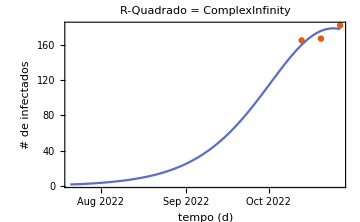

```mathematica
Quiet @ fitInfectedDynamic05["ParameterTable"]
Quiet @ fitInfectedDynamic05["BestFitParameters"]
Quiet @fitInfectedDynamic05["RSquared"]
Quiet @fitInfectedDynamic05["AdjustedRSquared"]
Quiet @FitWithDataPlot[fitInfectedDynamic05,{First@First@Normal[currentDynamic],First@Last@Normal[currentDynamic]} ]
```

### Simulação Total

```mathematica
AbsoluteTiming[fitInfectedDynamicAll=NonlinearModelFit[all,{infectedSolDynamic[t], {0<β && 0<α1<=1 && 0< α2<=1}},{{β,0.517}, {α1,0.729},{α2,0.692}},t, AccuracyGoal-> 3, WorkingPrecision-> 3,  PrecisionGoal -> 3, EvaluationMonitor:> Print["β=", β,"  .α1=",α1,"   .α2=",α2],Method-> {NMinimize, Method->{"NelderMead", "PostProcess"-> {"FindMinimum"}}}]]
```

```mathematica
Quiet @ fitInfectedDynamicAll["ParameterTable"]
Quiet @ fitInfectedDynamicAll["BestFitParameters"]
Quiet @fitInfectedDynamicAll["RSquared"]
Quiet @fitInfectedDynamicAll["AdjustedRSquared"]
Quiet @FitWithDataPlot[fitInfectedDynamicAll,{First@First@Normal[currentDynamic],First@Last@Normal[currentDynamic]} ]
```

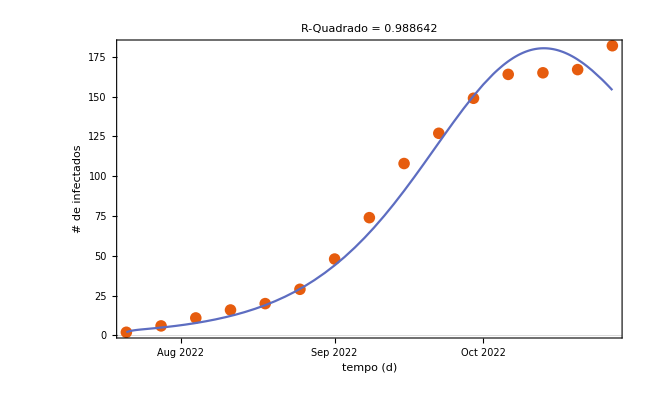

```mathematica
00001.260604874863131`3*10^-4
```

```mathematica
RealDigits[0.0001260604874863131`3.]
```

```mathematica
Chunk[list_,chunk_]:=Flatten[Partition[list,chunk][[#;;;;2]]]&/@{1,2}
```

```mathematica
fits ={fitInfectedDynamic, fitInfectedDynamic02, fitInfectedDynamic03, fitInfectedDynamic04, fitInfectedDynamic05}
```

```mathematica
JoinFittedDatePlot[fits_List,fitComplete_FittedModel,{dateMin_DateObject,dateMax_DateObject}]:=
Module[{plotAll,plotData,bands,cd, chunks},
cd=ColorData[108];
firstFit = First@fits;
lastFit = Last@fits;
plotAll={ToDataDate[dateMin,#1],#2}&@@@fitComplete["Data"];
plotData=Map[{ToDataDate[dateMin,#1],#2}&@@@#["Data"]&,fits];
bands[x_]=Quiet @ fitComplete["SinglePredictionBands",ConfidenceLevel->0.95]&/. t->x;
Show[DateListPlot[plotAll,Joined->True,PlotRange->All],
DateListPlot[plotData,Joined->False,PlotRange->All,PlotTheme->"Detailed"],
Plot[{fitComplete[ToModelTime[dateMin,FromAbsoluteTime@t]]&,
bands[ToModelTime[dateMin,FromAbsoluteTime@t]]},
{t,AbsoluteTime@dateMin,AbsoluteTime@dateMax},
PlotRange->All,
PlotStyle->{cd[2],None},
Filling->{2->{1}},
FillingStyle->{Opacity[0.5,Lighter@cd[2]]},
Exclusions->None],
PlotRange->All,
PlotRangePadding->{Automatic,{Scaled[0.03],Scaled[0.1]}},
FrameLabel->{"tempo (d)","# de infectados"},ImageSize->360,
PlotLabel->StringForm["Simulações com parâmetros ajustados"]]
//Labeled[#,Column[{LineLegend[{cd[1]},{"S00"}],PointLegend[{cd[2]},{"S01"}],PointLegend[{cd[3]},{"S02"}],PointLegend[{cd[4]},{"S03"}],PointLegend[{cd[5]},{"S04"}], PointLegend[{cd[6]},{"S05"}]},Left],Right]&]
```

```mathematica
JoinFittedDatePlot[fits,fitInfectedDynamicAll, {First@First@Normal[currentDynamic],First@Last@Normal[currentDynamic]}]
```

```mathematica
dateMin = First@First@Normal[currentDynamic];
dateMax = First@Last@Normal[currentDynamic];
bands[x_,t_]=Quiet @ Map[#["SinglePredictionBands",ConfidenceLevel->0.95]&/. t->x, fits]
```

## Modelo Final

```mathematica
lastFit = fitInfectedDynamic05 ;
lastParameters = Association@fitInfectedDynamic04["BestFitParameters"]
Normal@lastParameters[[2]]
(*lastFit["Data"]*)
resultsLastSimulation =Map[ParametricFunctionValues[#,lastParameters, {84,98,1}]&, asolDynamicBeta]
resultsLastSimulationMap = Map[Last[Last[Last[#]]]&,Normal@resultsLastSimulation]
```

```mathematica
modelSEIQRFinal = SetRateRules[modelSEIQRDynamicBeta, <|
NP[0] -> SP[0]+EP[0]+IP[0]+QP[0]+RP[0],  
β->Normal@lastParameters[[1]],
α1-> Normal@lastParameters[[2]],
α2->Normal@lastParameters[[3]]|>];
modelSEIQRFinal = SetInitialConditions[modelSEIQRFinal,
   <|
SP[98] -> resultsLastSimulationMap[[1]],
EP[98] -> resultsLastSimulationMap[[2]],
IP[98] -> resultsLastSimulationMap[[3]],
QP[98] -> resultsLastSimulationMap[[4]],
RP[98] -> resultsLastSimulationMap[[5]],
NIP[98] -> resultsLastSimulationMap[[6]],
PR[98] -> resultsLastSimulationMap[[7]],
    |>]; (* Subtrair do número da primeira semana epidemiológica*)
lsActualEquationsFinal = Join[modelSEIQRFinal["Equations"] //. KeyDrop[modelSEIQRFinal["RateRules"], {}], modelSEIQRFinal["InitialConditions"]];
ModelGridTableForm[modelSEIQRFinal]
ResourceFunction["GridTableForm"][List /@ lsActualEquationsFinal]
aSolFinal = NDSolve[lsActualEquationsFinal,{SP,EP,IP,QP, RP,NIP,PR},{t,99,161}]
```

```mathematica
aSolForPeaks = Association@Flatten@ParametricNDSolve[lsActualEquationsFinal,{SP,EP,IP,QP, RP,NIP,PR},{t,99,161},{β,α1,α2}]
```

```mathematica
allValues =Map[ParametricFunctionValues[#,lastParameters, {99,161,1}]&, aSolForPeaks]
peaks = Map[FindPeaks[Last/@#]&,allValues]
```

```mathematica
Clear[PadRealData];
PadRealData[aData:Association[(_String->_?VectorQ)..],incubationPeriod_?IntegerQ,infectiousPeriod_?IntegerQ]:=Block[{},Join[ConstantArray[0,incubationPeriod+infectiousPeriod],#]&/@aData];
```

```mathematica
optsFinal={PlotRange->All,PlotLegends->None,PlotTheme->"Detailed",PerformanceGoal->"Speed",ImageSize->800};
DynamicModule[{incubationPeriod=incubationPeriod,infectionPeriod=infectiousPeriod,nWeeks=40,padOffset=-7},
DynamicModule[{modelSEIQR=modelSEIQRFinal,lsFinal},
lsFinal = ParametricSolutionsPlots[modelSEIQR["Stocks"],#,None,nWeeks,"Together"->True,optsFinal]&/@GroupBy[Normal@aSolFinal,#[[1,1]]&,Association];
(*Show[List@Plot[Map[Identity[#]&,Values[aSolFinal]],{t,0,100}, PlotRange->All,PlotLegends->None,PlotTheme->"Detailed"], ListPlot[peaks,PlotStyle-> {Red,Black,Blue}]]]]*)
Show[lsFinal[[1,1]], ListPlot[Labeled[#,#]&/@peaks, PlotLabels->Above,PlotLegends->None]]
]
]
```

## Sensibilidade de parâmetro

FittedModel::precw: The precision of the argument function (MachinePrecision) is less than WorkingPrecision (3).

ParametricNDSolve::ihist: Conditions given at t = 0. will be interpreted as initial history functions for t/;t≤0..

FittedModel::precw: The precision of the argument function (MachinePrecision) is less than WorkingPrecision (3).

ParametricNDSolve::ihist: Conditions given at t = 0. will be interpreted as initial history functions for t/;t≤0..

FittedModel::precw: The precision of the argument function (MachinePrecision) is less than WorkingPrecision (3).

General::stop: Further output of FittedModel::precw will be suppressed during this calculation.

ParametricNDSolve::ihist: Conditions given at t = 0. will be interpreted as initial history functions for t/;t≤0..

General::stop: Further output of ParametricNDSolve::ihist will be suppressed during this calculation.

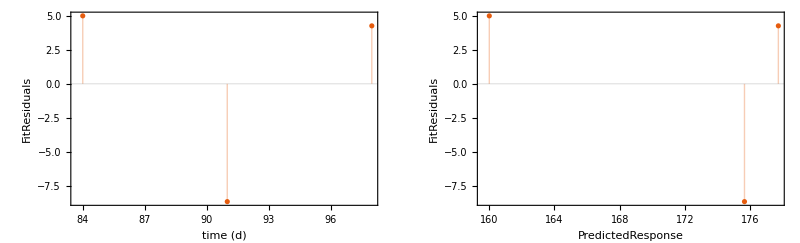

```mathematica
ResidualsPlot[fitInfectedDynamic05]
```

```mathematica
ClearAll[modelSensitivityPlot]
modelSensitivityPlot[modelIn:(_ParametricFunction[__]),fit_FittedModel,{{tMin_?NumberQ,tMax_?NumberQ},{yMin_?NumberQ,yMax_?NumberQ}},scale:{__?NumberQ}]:=Module[{model,sensitivities,cd=ColorData[108],params,t},params=fit["BestFitParameters"];
model=modelIn[t]/. params;
sensitivities=MapThread[model+(#2 {-1,1} D[modelIn,#1][t]/. params)&,{Keys@params,scale}];
TabView@MapThread[Function[{p,bands,sf},p->(Show[ListPlot[fit["Data"],PlotRange->All],Plot[{model,bands}//Evaluate,{t,tMin,tMax},PlotRange->All,PlotStyle->{cd[2],Lighter@cd[3],Lighter@cd[4]},Filling->{2->{{1},Opacity[0.5,Lighter@cd[3]]},3->{{1},Opacity[0.5,Lighter@cd[4]]}}],PlotRange->{All,{yMin,yMax}},PlotRangePadding->{Automatic,{Scaled[0.03],Scaled[0.1]}},FrameLabel->{"tempo (t) dias","# de infectados"},PlotLabel->"Sensibilidade do parâmetro",Epilog->{Inset[StringForm["Fator de Escala = ``",TraditionalForm[sf]],Scaled[{0.05,0.95}],{-1,1}]}]//Labeled[#,Column[{PointLegend[{cd[1]},{"Observado"}],LineLegend[{cd[2]},{"Calculado"}],SwatchLegend[{Opacity[0.5,Lighter@cd[3]]},{"Sensibilidade Negativa"}],SwatchLegend[{Opacity[0.5,Lighter@cd[4]]},{"Sensibilidade Positiva"}]},Left],Right]&)],{Keys@params,sensitivities,scale}]]
```

```mathematica
modelSensitivityPlot[infectedSolDynamic,fitInfectedDynamic05,{{0,100},{-10,190}},{0.354, 0.377,0.216}]
```

FittedModel::precw: The precision of the argument function (MachinePrecision) is less than WorkingPrecision (3).

ParametricNDSolve::ihist: Conditions given at t = 0. will be interpreted as initial history functions for t/;t≤0..

General::stop: Further output of ParametricNDSolve::ihist will be suppressed during this calculation.

FittedModel::precw: The precision of the argument function (MachinePrecision) is less than WorkingPrecision (3).

General::stop: Further output of FittedModel::precw will be suppressed during this calculation.

123